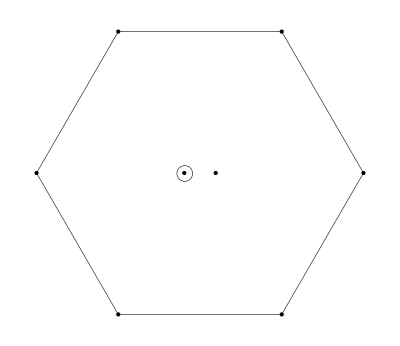

Y=0,  I_3=0

(ud-du)(d̄ū-ūd̄)+(us-su)(ūs̄-s̄ū)

```mathematica
(*-------------------------------*)
```

The current J:

(d_a^T Cγ^μ.(γ̄)^5 u_b-u_a^T Cγ^μ.(γ̄)^5 d_b) ((d̄)_a γ^μ.(γ̄)^5C((ū)_b)^T)+(u_a^T Cγ^μ.(γ̄)^5 d_b-d_a^T Cγ^μ.(γ̄)^5 u_b) ((ū)_a γ^μ.(γ̄)^5C((d̄)_b)^T)+1/2 (u_a^T C γ^μ d_b) ((d̄)_a γ^μ C((ū)_b)^T-(ū)_a γ^μ C((d̄)_b)^T)+1/2 (d_a^T C γ^μ u_b) ((ū)_a γ^μ C((d̄)_b)^T-(d̄)_a γ^μ C((ū)_b)^T)+(u_a^T Cγ^μ.(γ̄)^5 d_b) ((d̄)_b γ^μ.(γ̄)^5C((ū)_a)^T-(ū)_b γ^μ.(γ̄)^5C((d̄)_a)^T)+(d_a^T Cγ^μ.(γ̄)^5 u_b) ((ū)_b γ^μ.(γ̄)^5C((d̄)_a)^T-(d̄)_b γ^μ.(γ̄)^5C((ū)_a)^T)+1/2 (u_a^T C γ^μ d_b) ((d̄)_b γ^μ C((ū)_a)^T-(ū)_b γ^μ C((d̄)_a)^T)+1/2 (d_a^T C γ^μ u_b) ((ū)_b γ^μ C((d̄)_a)^T-(d̄)_b γ^μ C((ū)_a)^T)+1/2 (s_a^T C γ^μ u_b-u_a^T C γ^μ s_b) ((s̄)_a γ^μ C((ū)_b)^T)+(u_a^T Cγ^μ.(γ̄)^5 s_b) ((s̄)_a γ^μ.(γ̄)^5C((ū)_b)^T-(s̄)_b γ^μ.(γ̄)^5C((ū)_a)^T)+1/2 (s_a^T C γ^μ u_b-u_a^T C γ^μ s_b) ((s̄)_b γ^μ C((ū)_a)^T)+(s_a^T Cγ^μ.(γ̄)^5 u_b-u_a^T Cγ^μ.(γ̄)^5 s_b) ((ū)_a γ^μ.(γ̄)^5C((s̄)_b)^T)+1/2 (u_a^T C γ^μ s_b-s_a^T C γ^μ u_b) ((ū)_a γ^μ C((s̄)_b)^T)+(s_a^T Cγ^μ.(γ̄)^5 u_b) ((s̄)_b γ^μ.(γ̄)^5C((ū)_a)^T-(ū)_b γ^μ.(γ̄)^5C((s̄)_a)^T)+1/2 (u_a^T C γ^μ s_b-s_a^T C γ^μ u_b) ((ū)_b γ^μ C((s̄)_a)^T)-s_a^T Cγ^μ.(γ̄)^5 u_b(s̄)_a γ^μ.(γ̄)^5C((ū)_b)^T+u_a^T Cγ^μ.(γ̄)^5 s_b(ū)_b γ^μ.(γ̄)^5C((s̄)_a)^T

the Fierz rearranged J (to naively get the decay partten)

```mathematica
2 (ū(γ̄)^5 u) (s̄(γ̄)^5 s-d̄(γ̄)^5 d)+2 (ū 1u) (d̄ 1d-s̄ 1s)+3 (d̄(γ^μ).(γ̄)^5 d ū(γ^μ).(γ̄)^5 u)-3 (d̄(γ^μ).(γ̄)^5 u ū(γ^μ).(γ̄)^5 d)-3 (d̄ γ^μ d ū γ^μ u)+3 (d̄ γ^μ u ū γ^μ d)+2 (d̄(γ̄)^5 u ū(γ̄)^5 d)-2 (d̄ 1u ū 1d)-3 (s̄(γ^μ).(γ̄)^5 s ū(γ^μ).(γ̄)^5 u)+3 (s̄(γ^μ).(γ̄)^5 u ū(γ^μ).(γ̄)^5 s)+3 (s̄ γ^μ s ū γ^μ u)-3 (s̄ γ^μ u ū γ^μ s)-2 (s̄(γ̄)^5 u ū(γ̄)^5 s)+2 (s̄ 1u ū 1s)
```

Π(q^2)=
-(5 log(-q^2/μ^2) ⟨ ū u⟩ ⟨ d̄ Gd⟩)/(6 π^2)-(5 log(-q^2/μ^2) ⟨ d̄ d⟩ ⟨ ū Gu⟩)/(6 π^2)+(49 ⟨ d̄ Gd⟩ ⟨ ū Gu⟩)/(192 π^2 q^2)-(5 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ ū u⟩)/(9 π q^2)-(q^4 log(-q^2/μ^2) (m_d+m_s+6 m_u) ⟨ ū u⟩)/(6 π^4)-(q^4 (3 m_d+m_u) log(-q^2/μ^2) ⟨ d̄ d⟩)/(6 π^4)+(16 (12 m_d+m_u) ⟨ d̄ d⟩ ⟨ ū u⟩^2)/(9 q^2)+(16 (m_d+12 m_u) ⟨ d̄ d⟩^2 ⟨ ū u⟩)/(9 q^2)+(4 q^2 log(-q^2/μ^2) ⟨ d̄ d⟩ ⟨ ū u⟩)/(3 π^2)-(5 log(-q^2/μ^2) ⟨ ū u⟩ ⟨ s̄ Gs⟩)/(6 π^2)-(5 log(-q^2/μ^2) ⟨ s̄ s⟩ ⟨ ū Gu⟩)/(6 π^2)+(49 ⟨ s̄ Gs⟩ ⟨ ū Gu⟩)/(192 π^2 q^2)-(5 ⟨ GG ⟩ ⟨ s̄ s⟩ ⟨ ū u⟩)/(9 π q^2)-(q^4 (3 m_s+m_u) log(-q^2/μ^2) ⟨ s̄ s⟩)/(6 π^4)+(16 (12 m_s+m_u) ⟨ s̄ s⟩ ⟨ ū u⟩^2)/(9 q^2)+(16 (m_s+12 m_u) ⟨ s̄ s⟩^2 ⟨ ū u⟩)/(9 q^2)+(4 q^2 log(-q^2/μ^2) ⟨ s̄ s⟩ ⟨ ū u⟩)/(3 π^2)-(13 q^2 log(-q^2/μ^2) ⟨G^3⟩)/(576 π^6)+(q^4 log(-q^2/μ^2) ⟨ GG ⟩)/(32 π^5)-(11 q^8 g_s^2 log^2(-q^2/μ^2))/(55296 π^8)-(9397 q^8 g_s^2 log(-q^2/μ^2))/(5806080 π^8)-(q^8 log(-q^2/μ^2))/(320 π^6)

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for ρ_6=ρ_8=ρ_10=1

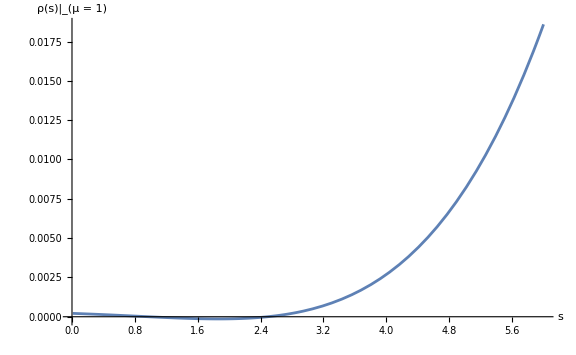
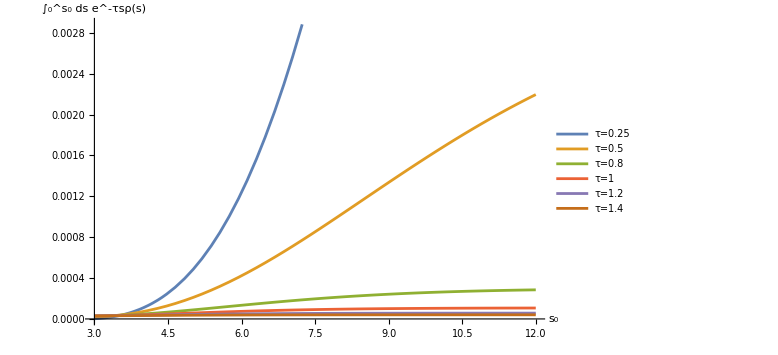

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for ρ_6=ρ_8=ρ_10=1

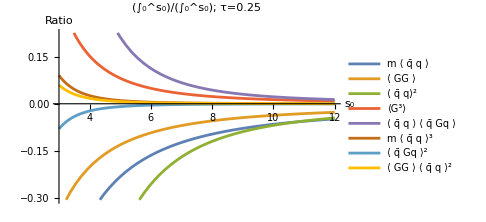
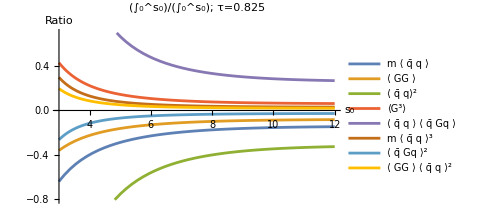
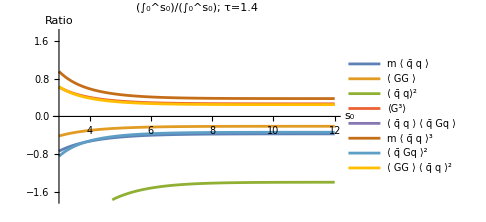

```mathematica
(*-------------------------------*)
```

ℛ^0 for ρ_6=ρ_8=ρ_10=1

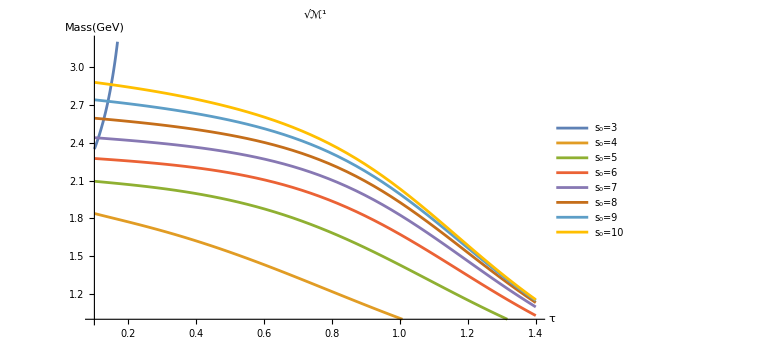
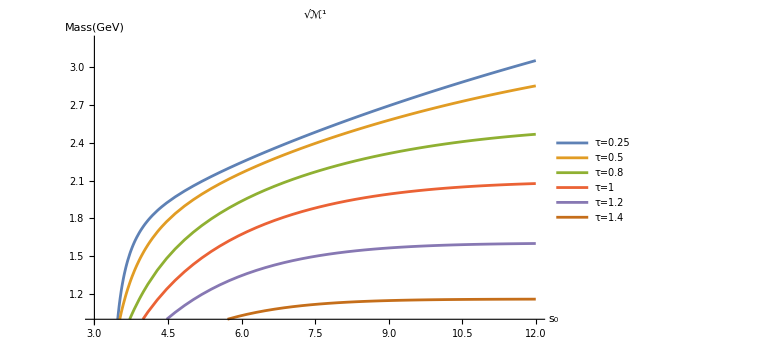

```mathematica
(*-------------------------------*)
```

ℛ^1 for ρ_6=ρ_8=ρ_10=1

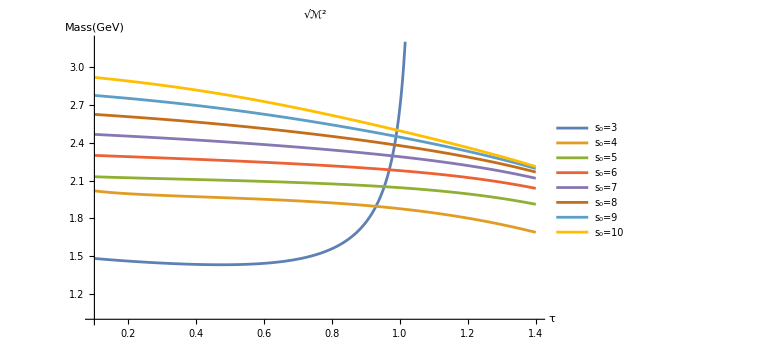
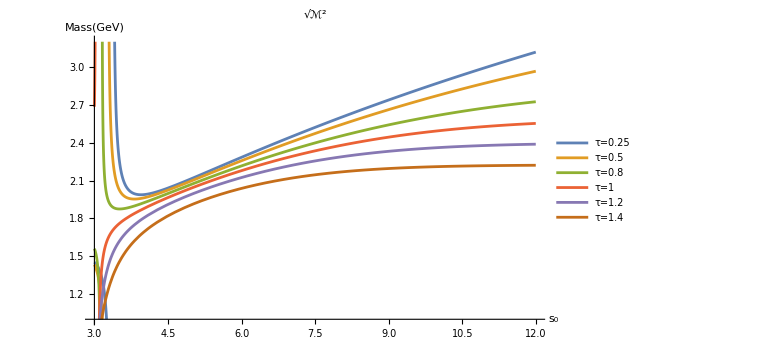

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for ρ_6=3, ρ_8=5, ρ_10=5

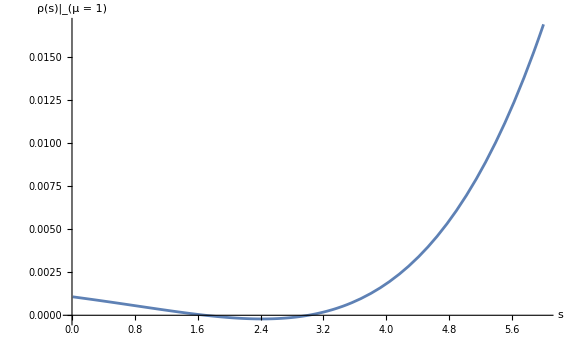
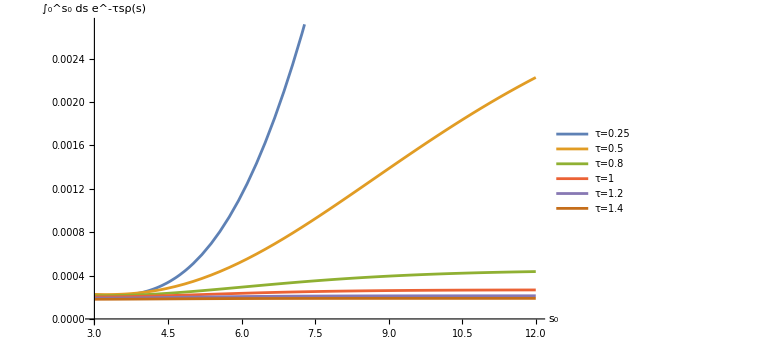

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for ρ_6=3, ρ_8=5, ρ_10=5

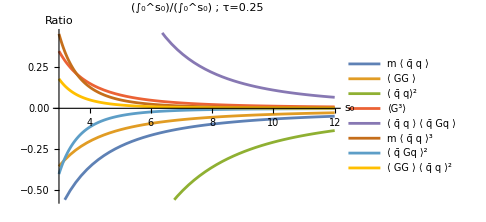
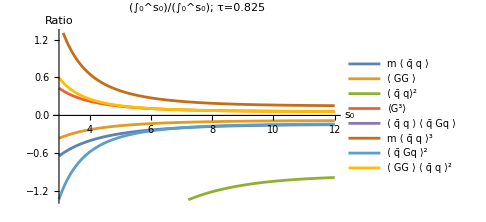
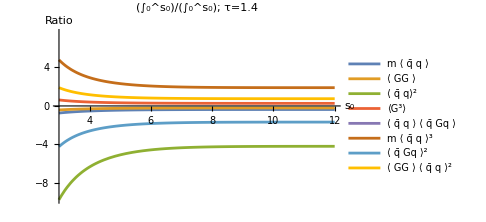

```mathematica
(*-------------------------------*)
```

ℛ^0 for ρ_6=3, ρ_8=5, ρ_10=5

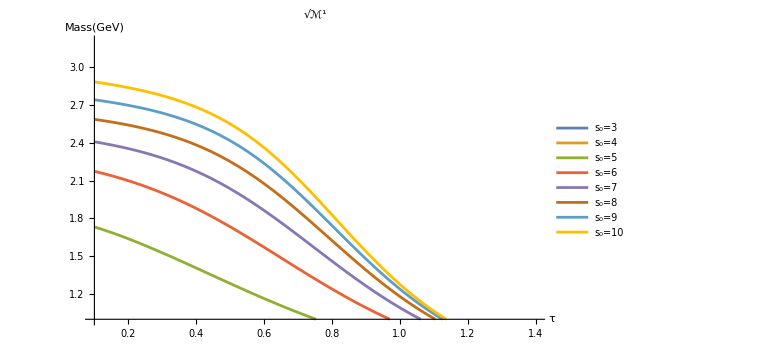
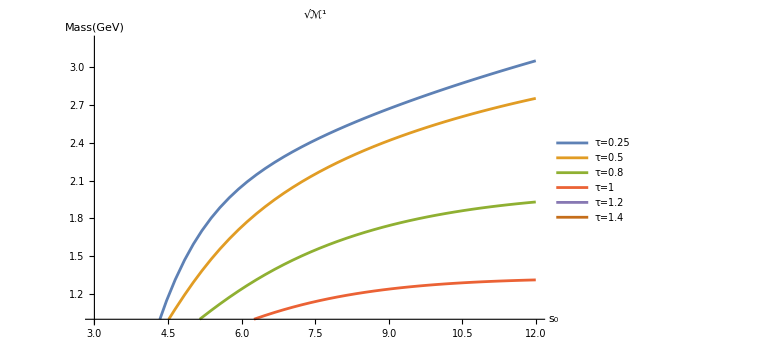

```mathematica
(*-------------------------------*)
```

ℛ^1 for ρ_6=3, ρ_8=5, ρ_10=5